## Summary: QuantumState

```mathematica
QuantumState[arg1,arg2]
```

arg1 is about the amplitudes (pure state) or corresponding matrix (e.g. density matrix), with respect to arg2, which contains basis info. One can use QuantumBasis[...] explicitly for arg2, or only give dimension info; which means the computational basis.

```mathematica
PacletInstall["Wolfram/QuantumFramework"]
```

PacletObject[…]

```mathematica
PacletObject[…]
```

PacletObject[…]

```mathematica
PacletInstall["https://wolfr.am/DevWQCF",ForceVersionInstall->True]
```

PacletObject[…]

```mathematica
PacletObject[…]
<<Wolfram`QuantumFramework`
```

PacletObject[…]

QuantumBasis::shdw: Symbol QuantumBasis appears in multiple contexts {Wolfram`QuantumFramework`,Global`}; definitions in context Wolfram`QuantumFramework` may shadow or be shadowed by other definitions.

QuantumState::shdw: Symbol QuantumState appears in multiple contexts {Wolfram`QuantumFramework`,Global`}; definitions in context Wolfram`QuantumFramework` may shadow or be shadowed by other definitions.

LibraryFunction::noopen: Cannot open libcotengra.

## Quantum Basis and State

In our Quantum Framework, a quantum state is defined with respect to a QuantumBasis. For pure states, the given input can be a list of amplitudes or an association with keys corresponding to basis elements and values as amplitudes.

Define a 2D quantum basis (computational):

```mathematica
QuantumBasis[2]
```

QuantumBasis[2]

```mathematica
QuantumBasis[2]
```

QuantumBasis[2]

Given the basis dimension n, the basis elements will be indexed by ket i with i=0,1,...,n-1:

```mathematica
%["ElementAssociation"]
```

<|0→{1,0},1→{0,1}|>(ElementAssociation)

```mathematica
QuantumState[{1,2,3,4}]["Basis"]["Association"]
```

<|00→{{1,0},{0,0}},01→{{0,1},{0,0}},10→{{0,0},{1,0}},11→{{0,0},{0,1}}|>

Use QuantumBasis[n,m] for n qudits of an m-dimensional quantum basis (whose overall dimension will be n^m). For example, let us define a 2×2×2-dimensional quantum basis (three qubits):

```mathematica
QuantumBasis[2,3]
```

QuantumBasis[…]

```mathematica
QuantumState["H"]["InputBasis"]["Association"]
```

<|1→1|>

```mathematica
QuantumState["RandomPure"]["BlochSpherePlot"]
QuantumState[{1,0},"X"]["BlochSpherePlot"]
```

-Graphics3D-

-Graphics3D-

```mathematica
QuantumBasis[2,3]
```

QuantumBasis[2,3]

```mathematica
%["Dimensions"]
```

QuantumBasis[2,3][Dimensions]

Use a list as QuantumBasis[{n_1,n_2,...,n_m}] for an n_1×n_2×n_2×...×n_m-dimensional Hilbert space of m qudits. For example, define a 3×5-dimensional quantum basis (two qudits):

```mathematica
QuantumBasis[{3,5}]
```

QuantumBasis[{3,5}]

```mathematica
%["Dimensions"]
```

A basis can also be defined by an association with the basis element names as keys and corresponding vectors as values:

```mathematica
QuantumBasis[<|a-> {1,ⅈ}, b-> {2,-ⅈ}|>]
```

```mathematica
QuantumBasis["X"]["Association"]
QuantumBasis["Y"]["Association"]
```

<|𝓍_+→{1/(√2),1/(√2)},𝓍_−→{1/(√2),-1/(√2)}|>

<|𝓎_+→{1/(√2),ⅈ/(√2)},𝓎_−→{1/(√2),-ⅈ/(√2)}|>

```mathematica
%["ElementNames"]
```

QuantumBasis[<|a→{1,ⅈ},b→{2,-ⅈ}|>][ElementNames]

There are many named basis objects built into the quantum framework, {"Computational", "PauliX", "PauliY", "PauliZ","Fourier", "Identity","Schwinger", "Pauli", "Dirac", "Wigner"}:

```mathematica
{QuantumBasis["PauliX"],QuantumBasis["Schwinger"],QuantumBasis["Bell"],QuantumBasis["Dirac"]}
```

After a basis object has been defined, it is straightforward to use it to construct quantum states and operators. A quantum state is represented by a QuantumState object and a quantum operator is represented by QuantumOperator.

For pure quantum states, a vector with elements as amplitudes along with the corresponding basis should be given in this format: QuantumState[amp_List,QuantumBasis[args]]. With no basis specified, the default basis will be the computational basis whose dimension depends on the amplitude vector.

Define a pure two-dimensional quantum state (qubit) in the Pauli-X basis:

```mathematica
QuantumState[{a,b},"X"]
```

```mathematica
Manipulate[Column[{Show[ParametricPlot3D[Table[{Sin[θ]Cos[ϕ], Sin[θ]Sin[ϕ],Cos[θ]},{ϕ,0,2π,π/8}],{θ,0,π},PlotStyle->{Black,Thin},Axes->False,Boxed->False,PlotRange->1,ImageSize->{550,370}],ParametricPlot3D[Table[{Sin[θ]Cos[ϕ], Sin[θ]Sin[ϕ],Cos[θ]},{θ,0,π,π/8}],{ϕ,0,2π},PlotStyle->{Black,Thin}],Graphics3D[{White,Opacity[.4],Sphere[{0,0,0},1],Opacity[1],Red,Tube[{{0,0,0},.8 {Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]}}],Cone[{.8 {Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]},{Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]}},.05],Darker[Green],Tube[{{0,0,0},.8 {Sin[θ1[θ,ϕ,g1]] Cos[ϕ1[θ,ϕ,g1]],Sin[θ1[θ,ϕ,g1]] Sin[ϕ1[θ,ϕ,g1]],Cos[θ1[θ,ϕ,g1]]}}],Cone[{.8 {Sin[θ1[θ,ϕ,g1]] Cos[ϕ1[θ,ϕ,g1]],Sin[θ1[θ,ϕ,g1]] Sin[ϕ1[θ,ϕ,g1]],Cos[θ1[θ,ϕ,g1]]},{Sin[θ1[θ,ϕ,g1]] Cos[ϕ1[θ,ϕ,g1]],Sin[θ1[θ,ϕ,g1]] Sin[ϕ1[θ,ϕ,g1]],Cos[θ1[θ,ϕ,g1]]}},.05],If[a==1,{Blue,Tube[{{0,0,0},.8 {Sin[θ2[θ,ϕ,g1,g2]] Cos[ϕ2[θ,ϕ,g1,g2]],Sin[θ2[θ,ϕ,g1,g2]] Sin[ϕ2[θ,ϕ,g1,g2]],Cos[θ2[θ,ϕ,g1,g2]]}}],Cone[{.8 {Sin[θ2[θ,ϕ,g1,g2]] Cos[ϕ2[θ,ϕ,g1,g2]],Sin[θ2[θ,ϕ,g1,g2]] Sin[ϕ2[θ,ϕ,g1,g2]],Cos[θ2[θ,ϕ,g1,g2]]},{Sin[θ2[θ,ϕ,g1,g2]] Cos[ϕ2[θ,ϕ,g1,g2]],Sin[θ2[θ,ϕ,g1,g2]] Sin[ϕ2[θ,ϕ,g1,g2]],Cos[θ2[θ,ϕ,g1,g2]]}},.05]}]},PlotRange->1,ImageSize->{550,370}]],

Graphics[{Text[Style[Row[{"|ψ> = ",N[ψ[θ,ϕ][[1]],4]," |0> + ",N[ψ[θ,ϕ][[2]],4]," |1>"}],Red,20],{0,1.5}],

Text[Style[Row[{Style[g[g1],Italic],"|ψ> = ",N[α1[θ,ϕ,g1],4]," |0> + ",N[β1[θ,ϕ,g1],4]," |1>"}],Darker[Green],20],{0,0}],

Text[Style[Row[{Style[g[g2]<>g[g1],Italic],"|ψ> = ",N[α2[θ,ϕ,g1,g2],4]," |0> + ",N[β2[θ,ϕ,g1,g2],4]," |1>"}],RGBColor[1-a,1-a,1],20],{0,-1.5}]

},PlotRange->{{-12,12},{-2,2}},ImageSize->{525,75}]}],

Row[{Control[{{θ,0,"θ"},0,π,π/8,Appearance->"Labeled"}],
Control[{{ϕ,0,"ϕ"},0,7π/8,π/8,Appearance->"Labeled"}]}],Row[{Spacer[20],Control[{{g1,1,"gate 1"},{1->"H",2->"X",3->"Y",4->"Z",5->"S",6->"T"},Setter}],Spacer[20],Control[{{a,0,"add gate 2?"},{0,1},Checkbox}],Spacer[20],
Control[{{g2,3,"gate 2"},{1->"H",2->"X",3->"Y",4->"Z",5->"S",6->"T"},Setter,Enabled->a==1}]}],
TrackedSymbols:>{θ,ϕ,g1,g2,a},Initialization:>(ψ[θ_,ϕ_]:={Cos[θ/2],Sin[θ/2] E^(I ϕ)};G[g1_]:={H,X,Y,Z,S,T}[[g1]];g[g1_]:={"H","X","Y","Z","S","T"}[[g1]];
H=1/(√2){{1,1},{1,-1}};X={{0,1},{1,0}};Y={{0,-I},{I,0}};Z={{1,0},{0,-1}};S={{1,0},{0,I}};T={{1,0},{0,E^(I π/4)}};ψ1[θ_,ϕ_,g1_]:=G[g1].ψ[θ,ϕ];
α1[θ_,ϕ_,g1_]:=Abs[ψ1[θ,ϕ,g1][[1]]];β1[θ_,ϕ_,g1_]:=ψ1[θ,ϕ,g1][[2]];
χ1[θ_,ϕ_,g1_]:=Im[Log[α1[θ,ϕ,g1]]];
θ1[θ_,ϕ_,g1_]:=2 ArcCos[α1[θ,ϕ,g1]];
ϕ1[θ_,ϕ_,g1_]:=Im[Log[β1[θ,ϕ,g1] E^(-I χ1[θ,ϕ,g1])]];
ψ2[θ_,ϕ_,g1_,g2_]:=G[g2].G[g1].ψ[θ,ϕ];
α2[θ_,ϕ_,g1_,g2_]:=Abs[ψ2[θ,ϕ,g1,g2][[1]]];
β2[θ_,ϕ_,g1_,g2_]:=ψ2[θ,ϕ,g1,g2][[2]];
χ2[θ_,ϕ_,g1_,g2_]:=Im[Log[α2[θ,ϕ,g1,g2]]];
θ2[θ_,ϕ_,g1_,g2_]:=2 ArcCos[α2[θ,ϕ,g1,g2]];
ϕ2[θ_,ϕ_,g1_,g2_]:=Im[Log[β2[θ,ϕ,g1,g2] E^(-I χ2[θ,ϕ,g1,g2])]];
)]
```

```mathematica
QuantumState[QuantumState[{a,b}],"X"]
```

QuantumState[QuantumState[{a,b}],X]

```mathematica
(a/(√2)+b/(√2))Subscript["𝓍", "+"]+(a/(√2)-b/(√2))Subscript["𝓍", "−"]
```

```mathematica
a Subscript["𝓍", "+"]Subscript["𝓍", "+"]+b Subscript["𝓍", "+"]Subscript["𝓍", "−"]+c Subscript["𝓍", "−"]Subscript["𝓍", "+"]+d Subscript["𝓍", "−"]Subscript["𝓍", "−"]
```

QuantumState[SparseArray[Automatic, {2, 2}, 0, {1, {{0, 2, 4}, {{1}, {2}, {1}, {2}}}, {a, b, c, d}}], QuantumBasis[Association["Input" -> QuditBasis[Association[{QuditName[I, "Dual" -> False], 1} -> 1]], 
    "Output" -> QuditBasis[Association[{QuditName[Subscript["𝓍", Interpretation["+", 1]], "Dual" -> False], 1} -> SparseArray[Automatic, {2}, 0, {1, {{0, 2}, {{1}, {2}}}, {1/Sqrt[2], 1/Sqrt[2]}}], 
       {QuditName[Subscript["𝓍", Interpretation["−", -1]], "Dual" -> False], 1} -> SparseArray[Automatic, {2}, 0, {1, {{0, 2}, {{1}, {2}}}, {1/Sqrt[2], -(1/Sqrt[2])}}]]], "Picture" -> "Schrödinger", "Label" -> None, 
    "ParameterSpec" -> {}]]]

```mathematica
QuantumState[{1,-1+ⅈ}, QuantumBasis["PauliX"]]
```

```mathematica
QuantumState[{1,-1+ⅈ},QuantumBasis["PauliX"]]
```

```mathematica
QuantumState[{{a,b},{c,d}},"X"]
```

a𝓍_+𝓍_++b𝓍_+𝓍_−+c𝓍_−𝓍_++d𝓍_−𝓍_−

```mathematica
%["Formula"]
```

a𝓍_+𝓍_++b𝓍_+𝓍_−+c𝓍_−𝓍_++d𝓍_−𝓍_−

If the basis is not specified, the default is the computational basis of 2^n dimension (n qubits):

```mathematica
QuantumState[{3,2ⅈ,1,-5}]
%["Amplitudes"]
```

```mathematica
QuditBasis /@Wolfram `QuantumFramework`PackageScope`$QuditBasisNames
```

Wolfram Global`QuantumFramework`PackageScope`$QuditBasisNames

If the vector has more than two elements, it is interpreted as an n-qubit state (by right-padding of zeros), unless the dimension is specified:

```mathematica
state= QuantumState[{2,0,ⅈ}]
```

```mathematica
state["Amplitudes"]
```

Same amplitude vector, but this time the dimension is specified:

```mathematica
state= QuantumState[{2,0,ⅈ},3];
state["Amplitudes"]
```

QuantumState::undefprop: property BlochSpherePlot is undefined for this state

QuantumState[…][BlochSpherePlot][Amplitudes][BlochSpherePlot]

Many named states are available for easy access:

```mathematica
Wolfram`QuantumFramework`PackageScope`$QuantumStateNames
```

{0,Zero,Up,1,One,Down,Plus,Minus,Left,Right,PsiPlus,PsiMinus,PhiPlus,PhiMinus,BasisState,Register,UniformSuperposition,UniformMixture,RandomPure,RandomMixed,GHZ,Bell,Dicke,W,Werner,Graph,BlochVector}

QuantumState[…]

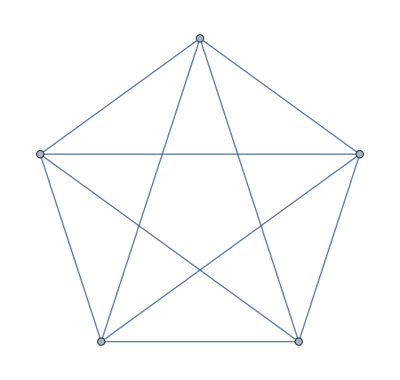

```mathematica
QuantumState["GHZ"]
RandomGraph[{5,10}]
```

```mathematica
QuantumState[{Graph, RandomGraph[{7, 5}]}]
```

```mathematica
QuantumState[…]
QuantumCircuitOperator[{Graph,RandomGraph[{5,5}]}]
```

QuantumState[…]

-Graphics-

Superposition of states

```mathematica
{QuantumState[{"UniformSuperposition",4}], QuantumState["PsiPlus"], QuantumState["GHZ"]}
```

{QuantumState[…],QuantumState[…],QuantumState[…]}

Using associations, one can create a superposition of states, with keys as a list of corresponding indexes and values as amplitudes. For example, let us create a superposition of three qubits (i.e. QuantumBasis[2,3]) as 1/(√2)(000+111):

```mathematica
ψ=QuantumState[<|{0,0,0}->1/(√2),{1,1,1}->1/(√2)|>,2,3]
```

QuantumState[…]

QuantumState::undefprop: property BlochSpherePlot is undefined for this state

QuantumState[…][BlochSpherePlot]

```mathematica
ψ["Formula"]
```

```mathematica
ψ["Dimensions"]
```

A different way of creating superposition is simply adding two quantum state objects. For example, the previous state can also be constructed as follows:

```mathematica
ψ2=(QuantumState[{"BasisState",{0,0,0}}]+QuantumState[{"BasisState",{1,1,1}}])/√2
```

```mathematica
ψ==ψ2
```

Once a built-in basis is specified, amplitudes correspond to the basis elements. For example, let's use Bell basis:

```mathematica
Normal/@QuantumBasis["Bell"]["ElementAssociation"]
```

```mathematica
ψ=QuantumState[{2,-ⅈ,1,3},QuantumBasis["Bell"]]
```

```mathematica
ψ["Amplitudes"]
```

We can also define a state by inputting a density matrix:

```mathematica
QuantumState[1/2(IdentityMatrix[2]+PauliMatrix[2])]
```

Do arithmetic with states

```mathematica
x QuantumState[{a,b}]+y QuantumState[{c,d}]
```

```mathematica
QuantumState[{"Werner",p,2}]["Formula"]
```

p/3 0000+1/6 (3-2 p)0101+1/6 (-3+4 p)0110+1/6 (-3+4 p)1001+1/6 (3-2 p)1010+p/3 1111

For pure states, one can get the corresponding normalized state vector:

```mathematica
%["Formula"]
```

Define a generic Bloch vector:

```mathematica
mat[r_]/;VectorQ[r]:=1/2(IdentityMatrix[2]+r.Table[PauliMatrix[i],{i,3}])
```

```mathematica
r={.1,.1,0};
state=QuantumState[mat[r]]
```

Test if it is a mixed state:

```mathematica
state["MixedStateQ"]
```

Calculate Von Neumann entropy:

```mathematica
state["VonNeumannEntropy"]
```

Purity:

```mathematica
state["Purity"]
```

A pure state (by normalizing the vector r):

```mathematica
state=QuantumState[mat[Normalize@r]]
```

Purity:

```mathematica
state["PureStateQ"]
```

Calculate Bloch spherical coordinates:

```mathematica
state["BlochSphericalCoordinates"]
```

A matrix that is not positive semidefinite (cannot be a density matrix in standard QM, but in ZX-formalism we can have situations like this):

```mathematica
mat[{1,2,0}]//PositiveSemidefiniteMatrixQ
```

A non-positive semidefinite matrix as state:

```mathematica
QuantumState[mat[{1,2,0}]]
```

For the matrices as an input, if no basis is given, the default basis will be computational:

```mathematica
m=RandomComplex[{-1-I,1+I},{8,8}];
ρ=ConjugateTranspose[m].m;
state=QuantumState[ρ]
```

```mathematica
state["Dimensions"]
```

Using ρ, define a quantum state in a 2×4-dimensional basis (note the number of qudits):

```mathematica
state=QuantumState[ρ,{2,4}]
```

```mathematica
state["Dimensions"]
```

Define a quantum state in 8D Hilbert space (one qudit only):

```mathematica
state=QuantumState[ρ,8]
```

```mathematica
state["Dimensions"]
```

One can also define a state in a given basis and then transform it into a new basis. For example, let us transform 0 in the computational basis into the basis of Pauli-X {+,-}:

```mathematica
ψ1=QuantumState[{1,0}];
ψ2=QuantumState[ψ1,"PauliX"]
```

Return amplitudes:

```mathematica
ψ1["Formula"]
ψ2["Formula"]
```

Note the states are the same, only defined in a different basis:

```mathematica
ψ1==ψ2
```

One can use QuantumTensorProduct to construct different states or operators. Create a tensor product of the plus state of three qubits +++:

```mathematica
ψ1=QuantumTensorProduct[QuantumState["Plus"],QuantumState["Plus"],QuantumState["Plus"]];
ψ1["Formula"]
```

Another way of defining +++ is to first define a basis and then assign amplitudes:

```mathematica
plusbasis=QuantumTensorProduct[QuantumBasis["PauliX"],QuantumBasis["PauliX"],QuantumBasis["PauliX"]];
```

```mathematica
ψ2=QuantumState[{0,0,0,0,0,0,0,1},plusbasis];
ψ2["Formula"]
```

```mathematica
ψ2==ψ1
```

Bloch vector as {r_x,r_y,r_z}:

```mathematica
QuantumState[{"BlochVector",{.4,.7,-.3}}]
```

```mathematica
%["BlochPlot"]
```

Adding quantum state as a String:

```mathematica
QuantumState["000"]
```

% == QuantumState[{1}, 2, 3]

```mathematica
Wolfram`QuantumFramework`PackageScope`$QuantumOperatorNames
```

{Identity,I,Permutation,Curry,Uncurry,Fourier,InverseFourier,XRotation,YRotation,ZRotation,U,Phase,P,RX,RY,RZ,R,Diagonal,GlobalPhase,PhaseShift,SUM,RootNOT,X,Y,Z,PauliX,PauliY,PauliZ,Shift,ShiftPhase,H,Hadamard,NOT,0,1,SWAP,RootSWAP,CSWAP,Fredkin,C,Controlled,C0,Controlled0,CX,CY,CZ,CH,CT,CS,CPHASE,CNOT,S,T,V,Toffoli,Deutsch,RandomUnitary,RandomHermitian,Spider,ZSpider,XSpider,WSpider,Measure,Encode,Copy,Cup,Cap,Switch,Discard,Multiplexer,WignerD,JX,JY,JZ,J+,J-,Double}

```mathematica
QuantumOperator[{"U",a,b,c}]
```

```mathematica
Cos[a/2]0 0-ⅇ^(ⅈ c) Sin[a/2]0 1+ⅇ^(ⅈ b) Sin[a/2]1 0+ⅇ^(ⅈ (b+c)) Cos[a/2]1 1
```

```mathematica
QuantumOperator[{"U",a,b,c}]["Matrix"] //MatrixForm
```

(Cos[a/2] | -ⅇ^(ⅈ c) Sin[a/2]
ⅇ^(ⅈ b) Sin[a/2] | ⅇ^(ⅈ (b+c)) Cos[a/2])

Functions to apply to quantum states
Quantum partial trace
Quantum distance
QuantumEntangledQ
QuantumEntanglementMonotone

```mathematica
state=QuantumState[{a,b,c,d}]
QuantumPartialTrace[state,{2}]["Formula"]//ComplexExpand
```

QuantumState[…]

(a Conjugate[a]+b Conjugate[b])00+(a Conjugate[c]+b Conjugate[d])01+(c Conjugate[a]+d Conjugate[b])10+(c Conjugate[c]+d Conjugate[d])11

```mathematica
p=QuantumState["RandomMixed"]
```

```mathematica
p["Operator"]
QuantumPartialTrace[QuantumBasis[{"X","Y"}],{2}]
```

p[Operator]

<|𝓍_+→{1/(√2),1/(√2)},𝓍_−→{1/(√2),-1/(√2)}|>

```mathematica
QuantumEntangledQ@QuantumState[{"Werner",1/2,2}]
```

False

```mathematica
QuantumEntangledQ@QuantumState[{"Werner",1/4,2}]
```

True

```mathematica
QuantumEntangledQ[QuantumState["GHZ"],{{1},{2}}]
```

False

```mathematica
QuantumEntanglementMonotone[QuantumState[{"Werner",1/4,2}],"LogNegativity"]
```

Log[3/2]/Log[2]

```mathematica
QuantumState[{"Werner",1/4,2}]==QuantumState[{1,2,3,4},4]["Bipartition"]
```

False

```mathematica
QuantumState[{1,2,3,4},4]==QuantumState[{1,2,3,4},4]["Bipartition"]
QuantumState[RandomReal[{0,1},12],12]["Bipartition",12]
```

True

QuantumState[…]

```mathematica
QuantumState["RandomPure"]["MatrixState"]["PureStateQ"]
```

True

```mathematica
QuantumState["RandomPure"]["MatrixState"]
QuantumState[{{a,b},{c,d}}]
```

QuantumState[…]

QuantumState[…]

```mathematica
QuantumState["RandomMixed"]["Properties"]
```

{Amplitude,Amplitudes,Association,Basis,Bend,BendDual,Bipartition,BlochCartesianCoordinates,BlochPlot,BlochSphericalCoordinates,Computational,Conjugate,ConjugateTranspose,Decompose,DecomposeWithAmplitudes,DecomposeWithProbabilities,DensityMatrix,Diagram,Dimension,Dimensions,Disentangle,Double,Dual,Eigenstates,Eigenvalues,Eigenvectors,ElementAssociation,ElementDimension,ElementDimensions,ElementNames,Elements,Entropy,FinalParameters,Formula,FullInputQudits,FullOutputQudits,FullQudits,FullSimplify,HasInputQ,InitialParameters,Input,InputBasis,InputDimension,InputDimensions,InputElementDimension,InputElementDimensions,InputElementNames,InputElements,InputMatrix,InputNameDimension,InputNameDimensions,InputQudits,InputRank,InputSize,InputTensor,Kind,Label,LabelHead,Matrix,MatrixDimensions,MatrixElementDimensions,MatrixNameDimensions,MatrixQ,MatrixRepresentation,MatrixState,Mixed,MixedStateQ,NameDimensions,Names,Norm,NormalElementNames,NormalizedAmplitudes,NormalizedDensityMatrix,NormalizedOperator,NormalizedProjector,NormalizedQ,NormalizedState,NormalizedStateVector,NumberQ,NumericQ,Operator,OrthogonalElements,Output,OutputBasis,OutputDimension,OutputDimensions,OutputElementDimension,OutputElementDimensions,OutputElementNames,OutputElements,OutputMatrix,OutputNameDimension,OutputNameDimensions,OutputQudits,OutputRank,OutputSize,OutputTensor,ParameterArity,Parameters,ParameterSpec,Physical,PhysicalQ,Picture,PrimeBasis,Probabilities,Probability,Projector,Projectors,Pure,PureEffects,PureMaps,PureStateQ,PureStates,Purify,Purity,QuditBasis,Qudits,Rank,Reverse,ReverseInput,ReverseOutput,Scalar,SchmidtBasis,SchmidtDecompose,Simplify,Size,SpectralBasis,Split,SplitDual,State,StateMatrix,StateTensor,StateType,StateVector,Tensor,TensorDimensions,TensorRepresentation,TensorReverseInput,TensorReverseOutput,Trace,TraceNorm,Transpose,Type,Unbend,UniformBasis,UnknownQ,Unpurify,VectorQ,VectorState,VonNeumannEntropy,Weights}

```mathematica
r=QuantumState[{"RandomPure",2}]
r["Decompose"]
Map[#["Computational"]["Formula"]&, r["Decompose"],{2}]
```

QuantumState[…]

{{QuantumState[…],QuantumState[…]},{QuantumState[…],QuantumState[…]}}

```mathematica
Map[#["Computational"]["Formula"]&, r["Decompose"],{2}]
Map[#["Formula"]["Formula"]&, r["Decompose"],{2}]
Total[QuantumTensorProduct/@r["Decompose"]]==r
```

{{(-0.655428+0. ⅈ)0+(-0.226788+0.555205 ⅈ)1,(-0.615029+0.494719 ⅈ)0+(0.528931-0.311809 ⅈ)1},{(-0.309892+0. ⅈ)0+(0.128066-0.313521 ⅈ)1,(-0.140999+0.597588 ⅈ)0+(-0.290165+0.734038 ⅈ)1}}

{{0.888409u_1[Formula],v_1[Formula]},{0.459052u_2[Formula],v_2[Formula]}}

True

```mathematica
#["Formula"]&/@r["Disentangle"]
Total[r["Disentangle"]]==r
```

{0.888409u_1 v_1,0.459052u_2 v_2}

True

```mathematica
QuantumPartialTrace[%,{2}]==r
```

QuantumPartialTrace[True,{2}]==QuantumState[…]

```mathematica
r["Purify"]
```

QuantumState[…]

```mathematica
QuantumState[{a1,a2,a3,a4}]
QuantumState[{a1,a2,a3,a4}]["Permute",Cycles[{{1,2}}]]
```

QuantumState[…]

QuantumState[…]

```mathematica
QuantumState["PhiPlus"]
```

QuantumState[…]

```mathematica
proj=QuantumState["PhiPlus"]["Projector"]
op=QuantumState["PhiPlus"]["Operator"]
```

QuantumState[…]

QuantumOperator[…]

```mathematica
r=QuantumState[{"RandomPure",2}]
proj[r]==QuantumState["PhiPlus"]
op[r]==QuantumState["PhiPlus"]


QuantumState["1"]["Diagram"]
QuantumState["10"]["Diagram"]
QuantumState["101"]

QuantumCircuitOperator[{"H",{"1"}}]["Diagram"]
```

QuantumState[…]

True

True

-Graphics-

-Graphics-

QuantumState[…]

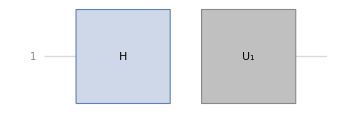

```mathematica
Wolfram`QuantumFramework`PackageScope`$QuantumOperatorNames
Wolfram`QuantumFramework`PackageScope`$QuditBasisNames
Wolfram`QuantumFramework`PackageScope`$QuantumStateNames
Wolfram`QuantumFramework`PackageScope`$QuantumChannelNames
Wolfram`QuantumFramework`PackageScope`$QuantumMeasurementOperatorNames
Wolfram`QuantumFramework`PackageScope`$QuantumCircuitOperatorNames
Wolfram`QuantumFramework`PackageScope`$QuantumDistances
Wolfram`QuantumFramework`PackageScope`$QuantumEntanglementMonotones
```

-Graphics-

-Graphics-

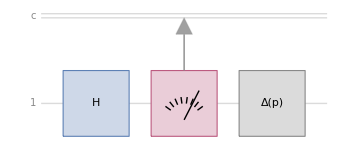

```mathematica
QuantumMeasurementOperator["X"]["POVM"]["Diagram"]
QuantumChannel[{"Depolarizing",p}]["Diagram"]
QuantumCircuitOperator[{"H",{1},QuantumChannel[{"Depolarizing",p}]}]["Diagram"]
```